```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

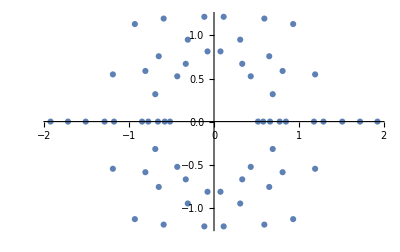

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
fastRootCalculate[n_Integer,x_:Unique[]]:=With[{
poly=1+#+Tuples[{1,-1},n-1]. #^Range[2,n]&,
solve=If[$VersionNumber<12.3,x/.NSolve@##&,NSolveValues],
mirror=If[n>3,Thread,Identity]@Join[#,-#]&,
map=If[n>5,ParallelMap,Map],
k=Floor[n/4]-$KernelCount},
If[k>0&&k<5,LaunchKernels@k];
map[solve[#==0,x]&,poly@x]//mirror]
```

```mathematica
Block[{r,k=4-$KernelCount},If[k>0,LaunchKernels@k];
AbsoluteTiming[r=fastRootCalculate[10];]]
```

{0.428502,Null}

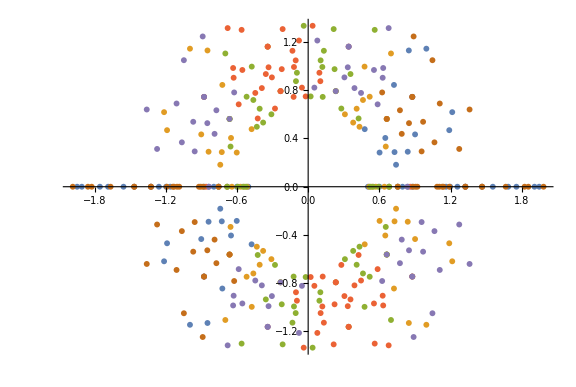

```mathematica
ComplexListPlot[fastRootCalculate[6],ImageSize->Large]
```

```mathematica
displayRoots[n_]:=With[{
p=fastRootCalculate[n],
r=PlotRange->4.1{#,#}2^-{1,3/2}&[{-1,1}],
d=Round[If[n>5,999/(n+7),25](83/100)^n,1/2],
f=FontSize->If[n>5,120,(n+7)3],
w=ImageSize->If[n>5,5000,(n+7)125]},
With[{
c=If[n>5,{Hue[#/n],Point@ReIm@p[[#]]}&,40/(n+7)],
s=AbsolutePointSize@If[n<19,d,1/2],
l=PlotLabel->Style[Row@{"n = ",n},f],
a=AspectRatio->Tr@Ratios[Differences/@Last@r]},
If[n>5,
Graphics[{s}~Join~Flatten@Array[c,n],w,r,l],
ComplexListPlot[p,PlotStyle->s,a,w,r,l]~Magnify~c]]
]
```

```mathematica
Block[{r},AbsoluteTiming[r=fastRootCalculate@18;]]
```

{139.917,Null}

```mathematica
Block[{g=Table[Graphics[],20],a=AbsoluteTiming,t,k},
k=4-$KernelCount;t=Table[{0,0,0},Length@g];
If[k>0,LaunchKernels@k;Pause@1];
Do[k=ToString@i<>".png";
Print["Calculating roots: n = "<>First[k~StringSplit~"p"]];
t[[i]]=First/@{
a[g[[i]]=displayRoots[i];Print["Rendering: "<>k];],
a[g[[i]]=Rasterize[g[[i]],"Image",Background->None];],
a[Export[k,g[[i]]]; (* memory clean-up & save *) g[[i]]=i]},
{i,Length@g}];
CloseKernels[];
k={n,"Calculations","Graphics & Scale","Save"};
Column@{"",
Style["Timing Values (sec):",FontSize->14,FontWeight->Bold],"",
TableForm[MapIndexed[#2~Join~#1&,t],TableHeadings->{None,k}]}
]
```

Timing Values (sec):

n | Calculations | Graphics & Scale | Save
1 | 1.53778 | 9.10223 | 1.5407
2 | 0.948085 | 0.333336 | 0.646625
3 | 0.0375705 | 0.320516 | 0.614589
4 | 0.0384976 | 0.321538 | 0.610527
5 | 0.105262 | 0.327722 | 0.606783
6 | 0.188209 | 0.317891 | 0.619202
7 | 0.0962114 | 0.320143 | 0.624946
8 | 0.15687 | 0.349102 | 0.666462
9 | 0.282418 | 0.422168 | 0.668688
10 | 0.534843 | 0.570936 | 0.718631
11 | 1.11695 | 0.927695 | 0.786318
12 | 2.22101 | 1.53835 | 0.947521
13 | 4.63396 | 2.95507 | 1.08659
14 | 9.64957 | 6.05802 | 1.19929
15 | 20.5326 | 9.32765 | 0.69432
16 | 42.3323 | 19.7582 | 0.927354
17 | 88.5235 | 41.9776 | 1.04109
18 | 184.091 | 89.8458 | 1.30036
19 | 388.22 | 181.356 | 1.27213
20 | 788.43 | 404.742 | 5.55213

```mathematica
Block[{g=Table[Graphics[],20],a=AbsoluteTiming,t},
t=Table[0,Length@g+1];
Do[t[[i]]=First@a[g[[i]]=Import[ToString@i<>".png"];],{i,Length@g}];
t[[-1]]=First@a[Export["roots.gif",g,"DisplayDurations"->3/2];];
TableForm[MapIndexed[#2~Append~#1&,t],
TableHeadings->{None,{n,"Import/Export time"}}]]
```

n | Import/Export time
1 | 1.32816
2 | 0.172968
3 | 0.156913
4 | 0.170532
5 | 0.152374
6 | 0.174053
7 | 0.189223
8 | 0.207529
9 | 0.223069
10 | 0.278304
11 | 0.32641
12 | 0.386027
13 | 0.460916
14 | 0.584735
15 | 0.189343
16 | 0.21444
17 | 0.249272
18 | 0.296658
19 | 0.315117
20 | 0.287223
21 | 19.0122